```mathematica
λ=635; (*laser wavelength in nm*)
w=1000;(*slit width in nm*)
d=1;(*distance between slits in nm*)
n=1;(*number of slits*)
I0=1;
Ix[x]=I0(Sin[(n*π*d)/λ Sin[x]]/Sin[(π*d)/λ Sin[x]])^2(Sin[(π*w)/λ Sin[x]]/((π*w)/λ Sin[x]))^2;
```

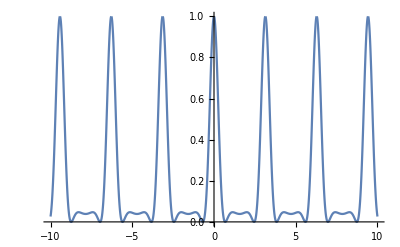

```mathematica
Plot[Ix[x],{x,-10,10},PlotRange->All]
```

```mathematica
Ix[x_?NumberQ,sx_?NumberQ/;sx>0,sy_?NumberQ/;sy>0,x0_?NumberQ,y0_?NumberQ] = Piecewise[{{sy(2 BesselJ[1,(x-x0)/sx]/((x-x0)/sx))^2+y0,x≠x0}},sy+y0];
Imx[x_?NumberQ,sx_?NumberQ/;sx>0,sy_?NumberQ/;sy>0,x0_?NumberQ,y0_?NumberQ] = Piecewise[{{Min[sy(2 BesselJ[1,(x-x0)/sx]/((x-x0)/sx))^2+y0,255],x≠x0}},sy+y0];
Ix3D[x_?NumberQ,y_?NumberQ,sx_?NumberQ/;sx>0,sy_?NumberQ/;sy>0,sz_?NumberQ/;sz>0,x0_?NumberQ,y0_?NumberQ,z0_?NumberQ] = Piecewise[{{sz(2 BesselJ[1,√(((x-x0)/sx)^2+((y-y0)/sy)^2)]/(√(((x-x0)/sx)^2+((y-y0)/sy)^2)))^2+z0,x≠x0||y≠y0}},sz+z0];
Imx3D[x_?NumberQ,y_?NumberQ,sx_?NumberQ/;sx>0,sy_?NumberQ/;sy>0,sz_?NumberQ/;sz>0,x0_?NumberQ,y0_?NumberQ,z0_?NumberQ] = Piecewise[{{Min[sz(2 BesselJ[1,√(((x-x0)/sx)^2+((y-y0)/sy)^2)]/(√(((x-x0)/sx)^2+((y-y0)/sy)^2)))^2+z0,255],x≠x0||y≠y0}},sz+z0];

cImx3D=Compile[{x_?Real,y_?Real,sx_?Real/;sx>0,sy_?Real/;sy>0,sz_?Real/;sz>0,x0_?Real,y0_?Real,z0_?Real},
Piecewise[{{Min[sz ((2 BesselJ[1,√(((x-x0)/sx)^2+((y-y0)/sy)^2)])/(√(((x-x0)/sx)^2+((y-y0)/sy)^2)))^2+z0,255], x≠x0||y≠y0}, {sz+z0, True}}],
CompilationTarget->"C",
RuntimeAttributes->{Listable},
Parallelization->True]
```

CompiledFunction[…]

```mathematica
Manipulate[DensityPlot[Ix3D[x,y,sx,sy,sz,x0,y0,z0],{x,0,128},{y,0,128},PlotRange->{0,255},PlotPoints->50],{{sx,2},1,8},{{sy,2},1,8},{{sz,6000},0,100000},{{x0,64},-128,128},{{y0,64},-128,128},{{z0,0},0,255}]
```

```mathematica
observation = Import["C:\\Users\\Benjamin\\OneDrive\\Documents\\UQAR\\2017 Été\\Stage I\\mathematica-test\\points.data", "Table"];
```

```mathematica
fittedIx=NonlinearModelFit[observation[[All,2]],Ix[x,sx,sy,x0,y0],{{sx,7},{sy,255},{x0,127}, {y0,0}},x]
```

FittedModel[Ix[x,9.97282,288.753,131.385,2.78753]]

```mathematica
fittedImx=NonlinearModelFit[observation[[All,2]],Imx[x,sx,sy,x0,y0],{{sx,7},{sy,255},{x0,127}, {y0,0}},x]
```

FittedModel[Imx[x,6.10525,1429.67,131.333,4.15606]]

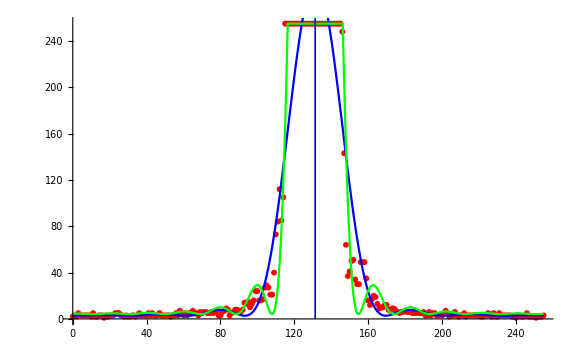

```mathematica
Show[{
ListPlot[observation,PlotRange->All,PlotStyle->Red],
Plot[fittedIx[x],{x,0,255},PlotRange->All, PlotStyle->Blue],
Plot[fittedImx[x],{x,0,255},PlotRange->All, PlotStyle->Green]},
Epilog-> {
Blue,Line[{{x0/.fittedIx["BestFitParameters"],0},{x0/.fittedIx["BestFitParameters"],300}}],
Blue,Line[{{x0/.fittedImx["BestFitParameters"],0},{x0/.fittedImx["BestFitParameters"],300}}]
},
ImageSize->Large]
```

```mathematica
laserdata=Import["C:\\Users\\Benjamin\\OneDrive\\Documents\\UQAR\\2017 Été\\Stage I\\mathematica-test\\laser3.bmp", "RawData"];
side=Length[laserdata];
size=side*side;
lasermatrix=Table[0,size,3];
lasermatrix⟦All,1⟧=Table[Quotient[i,side],{i,0,size-1}];
lasermatrix⟦All,2⟧=Table[Mod[i,side],{i,0,size-1}];
lasermatrix⟦All,3⟧=Flatten[laserdata];
```

```mathematica
fittedIx3D=NonlinearModelFit[lasermatrix,Ix3D[x,y,sx,sy,sz,x0,y0,z0],{{sx,2},{sy,2},{sz,255},{x0,side/2},{y0,side/2} ,{z0,4}},{x,y}]
```

FittedModel[Ix3D[x,y,5.35441,7.16696,210.178,58.4313,69.3102,4.83073]]

```mathematica
fittedImx3D=NonlinearModelFit[lasermatrix,Imx3D[x,y,sx,sy,sz,x0,y0,z0],{{sx,2},{sy,2},{sz,65536},{x0,side/2},{y0,side/2} ,{z0,4}},{x,y}]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[Imx3D[x,y,1.68528,2.04865,8780.42,59.4503,67.152,5.91017]]

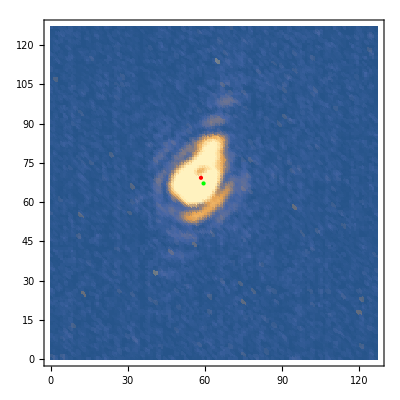

```mathematica
ListDensityPlot[lasermatrix,PlotRange->All,
Epilog->{
Red,Point[{x0/.fittedIx3D["BestFitParameters"],y0/.fittedIx3D["BestFitParameters"]}],
Green,Point[{x0/.fittedImx3D["BestFitParameters"],y0/.fittedImx3D["BestFitParameters"]}]
}]
```

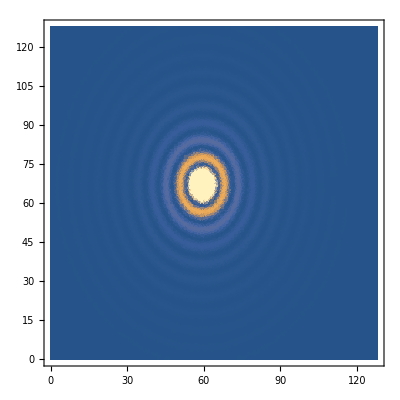

```mathematica
DensityPlot[fittedImx3D[x,y],{x,0,128},{y,0,128},PlotRange->{0,255},PlotPoints->50]
```